# Pentagons

In this notebook, we figure out the basics of drawing shapes in mathematica and automating replacement rules

## Drawing pentagons

```mathematica
l
```

Line[{{0,0},{1,0}}]

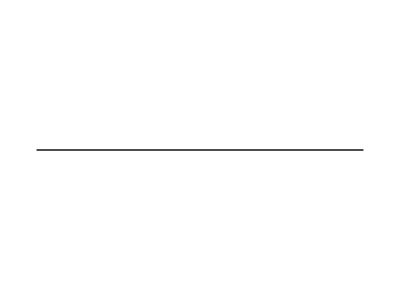

```mathematica
Graphics[l=Line[{{0,0},{1,0}}]]
```

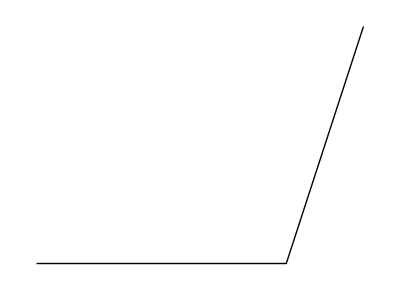

```mathematica
nextCoords[coords1_,coords2_,angle_]:=Module[
{coords3},
coords3 = 2*coords2 - coords1;
RotationTransform[angle,coords2][coords3]
]

point1 = {0,0}; point2={1,0};
Graphics[Line[{point1,point2,nextCoords[point1,point2,Pi-3Pi/5]}]]
```

```mathematica
pentagon[coords1_,coords2_]:=Module[
{i,l={coords1,coords2}},
For[i=0, i<3, i++,
AppendTo[l,nextCoords[l⟦-2⟧,l⟦-1⟧,2Pi/5]];
];Append[l,coords1]
]
```

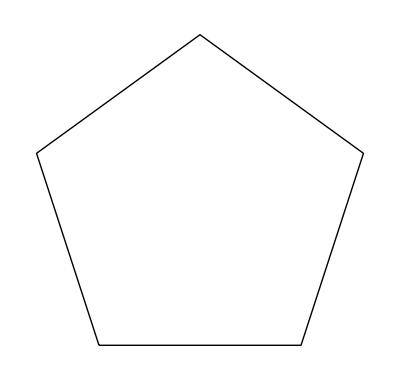

```mathematica
point1 = {0,0}; point2={1,0};
Graphics[Line[pentagon[point1,point2]]]
```

## Replacing smaller pentagons